```mathematica
ClearAll["global`*"]
```

## Solution in external harmonic potential

```mathematica
M={{-(κ+k)/γ,κ/γ},{κ/γ,-κ/γ}};
```

```mathematica
MatrixForm[M];
```

```mathematica
expM=MatrixExp[M*(-tp)];
```

```mathematica
covar=Integrate[expM.{{2*Subscript[T, c]/γ,0},{0,2*Subscript[T, h]/γ}}.Transpose[expM],{tp,-Infinity,0},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
FullSimplify[covar/.{Subscript[T, c]->Subscript[T, h]},Assumptions->{γ>0,k>0,κ>0}];
```

```mathematica
P[x_,y_,kk_]:=Simplify[Exp[-1/2*{x,y}.Inverse[covar].{x,y}]]/.{k->kk};
```

```mathematica
Log[P[x,y,k]];
```

```mathematica
expo = -((k+2 κ) (κ (k y^2+(x-y)^2 κ) Subscript[T, c]+(k^2 x^2+k x (3 x-2 y) κ+(x-y)^2 κ^2) Subscript[T, h]))/(2 (κ^2 Subscript[T, c]^2+(k^2+4 k κ+2 κ^2) Subscript[T, c] Subscript[T, h]+κ^2 Subscript[T, h]^2));
```

## Patching and normalization

```mathematica
SubMinus[k]=2*Subscript[U, 0]/L^2;
```

```mathematica
SubPlus[k]=2*Subscript[U, 0]/l^2;
```

```mathematica
potential= (Piecewise[{{SubMinus[k]*(x+L)^2/2,x≤0},{SubPlus[k]*(x-l)^2/2,x>0}}]/.{l->Subscript[λ, r]*d,L->Subscript[λ, l]*d})/.{d->1,Subscript[U, 0]->1}
```

Piecewise[{{(x+λ_l)^2/λ_l^2, x≤0}, {(x-λ_r)^2/λ_r^2, x>0}, {0, True}}]

```mathematica
SubMinus[f]=FullSimplify[Integrate[P[x,y,SubMinus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
SubPlus[f]=FullSimplify[Integrate[P[x,y,SubPlus[k]],{y,-Infinity,Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{x->0})==SubPlus[A]*(SubPlus[f]/.{x->0})&&SubMinus[A]*Integrate[SubMinus[f],{x,-L,0},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]+SubPlus[A]*Integrate[SubPlus[f],{x,0,l},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}]==1,{SubMinus[A],SubPlus[A]}],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

## Current density maps

```mathematica
Subscript[p, left]=Simplify[((SubMinus[A]/. SubMinus[exprA])* P[x,y,SubMinus[k]]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2})/.{d->1,Subscript[U, 0]->1,γ->1},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[p, right]=Simplify[((SubPlus[A]/. SubPlus[exprA])* P[x,y,SubPlus[k]]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2})/.{d->1,Subscript[U, 0]->1,γ->1},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
prob = Piecewise[{{Subscript[p, left],x≤0},{Subscript[p, right],x>0}}];
```

```mathematica
probplot = prob/.{y->s+x,Subscript[λ, l]->0.7,Subscript[λ, r]->0.3,κ->1,Subscript[T, 1]->0.1,Subscript[T, 2]->1.0};
```

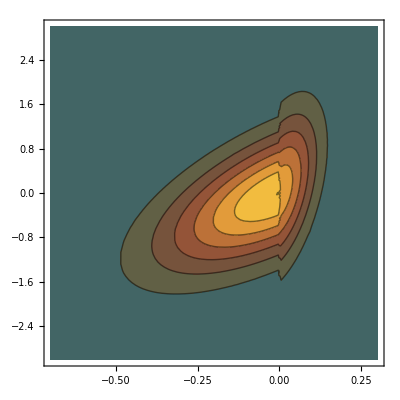

```mathematica
ContourPlot[probplot,{x,-0.7,0.3},{s,-3,3},PlotRange->{{-0.7,0.3},{-3,3},{0,1.5}},Exclusions->None,ColorFunction->"Autumn"]
```

```mathematica
probs = prob/.{y->(s+x)};
```

```mathematica
jx =-probs*(D[potential,x]-s*κ)-Subscript[T, 1]*D[probs,{x,1}]-Subscript[T, 1]*D[probs,{s,1}];
```

```mathematica
js = (probs*(D[potential,x]-2*κ*s))-Subscript[T, 1]*D[probs,{x,1}]-(Subscript[T, 1]+Subscript[T, 2])*D[probs,{s,1}];
```

```mathematica
Subscript[T, c]= 0.5
```

0.5

```mathematica
jxplot = jx/.{Subscript[λ, l]->0.7,Subscript[λ, r]->0.3,κ->1,Subscript[T, 1]->Subscript[T, c],Subscript[T, 2]->1.0};
jsplot = js/.{Subscript[λ, l]->0.7,Subscript[λ, r]->0.3,κ->1,Subscript[T, 1]->Subscript[T, c],Subscript[T, 2]->1.0};
```

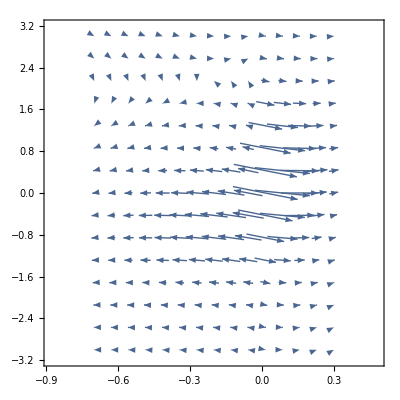

```mathematica
VectorPlot[1*{jxplot,jsplot},{x,-0.7,0.3},{s,-3,3},VectorScale->{Small,1/6,Automatic}]
```

```mathematica
mvx = MinValue[jxplot,{x,s}];
```

```mathematica
mxvx = MaxValue[jxplot,{x,s}];
```

```mathematica
mvs = MinValue[jsplot,{x,s}];
```

```mathematica
mxvs = MaxValue[jsplot,{x,s}];
```

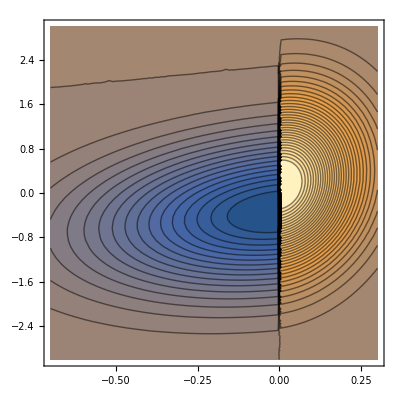

```mathematica
ContourPlot[1*jxplot,{x,-0.7,0.3},{s,-3,3},PlotRange->{{-0.7,0.3},{-3,3},{mvx,mxvx}},Exclusions->None,Contours->50]
```

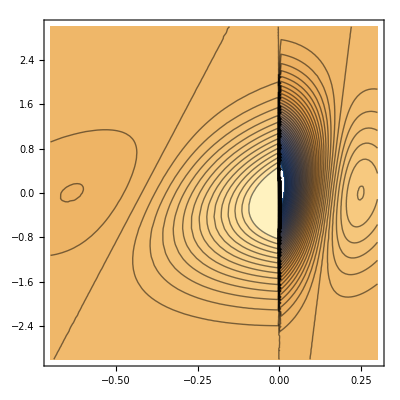

```mathematica
ContourPlot[1*jsplot,{x,-0.7,0.3},{s,-3,3},PlotRange->{{-0.7,0.3},{-3,3},{mvs,mxvs}},Exclusions->None,Contours->50]
```

## Current

```mathematica
Subscript[J, R] = Simplify[-(k*x+κ*(x-y))/γ*P[x,y,k]-Subscript[T, c]/γ*D[P[x,y,k],x],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
{{SubPlus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->l,k->SubPlus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
{{SubMinus[exprr]}}=FullSimplify[Solve[(Subscript[J, R]/P[x,y,k]/.{x->-L,k->SubMinus[k]})==0,y],{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, right]=Simplify[Integrate[SubPlus[A]*Subscript[J, R]/.{x->l,k->SubPlus[k],SubPlus[exprA]},{y,y/.{SubPlus[exprr]},Infinity},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, left]=Simplify[Integrate[SubMinus[A]*Subscript[J, R]/.{x->-L,k->SubMinus[k],SubMinus[exprA]},{y,-Infinity,y/.{SubMinus[exprr]}},Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, total]= Simplify[Subscript[J, right]+Subscript[J, left],Assumptions->{γ>0,κ>0,Subscript[U, 0]>0,l>0,L>0,Subscript[T, h]>Subscript[T, c]>0}];
```

```mathematica
Subscript[J, unitless]=Simplify[ Subscript[J, total]/.{Subscript[T, c]->Subscript[T, 1]*Subscript[U, 0],Subscript[T, h]->Subscript[T, 2]*Subscript[U, 0],L->Subscript[λ, l]*d,l->Subscript[λ, r]*d,κ->κ*Subscript[U, 0]/d^2},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, paper]= Simplify[Subscript[J, unitless]/.{Subscript[T, 1]->T*(1-δ),Subscript[T, 2]->T*(1+δ)},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,T>0,δ>0,d>0}];
```

```mathematica
Subscript[J, exp]= Simplify[Subscript[J, paper]/.{κ->q*T},{γ>0,κ>0,Subscript[U, 0]>0,λ>0,d>0,Subscript[T, 1]>0,Subscript[T, 2]>0,δ>0,Subscript[U, 0]>0}];
```

```mathematica
Subscript[J, sub]=Simplify[Subscript[J, unitless]/.{Subscript[U, 0]->1,d->1,Subscript[λ, l]->0.1,Subscript[λ, r]->0.9,γ->1},{κ>0,Subscript[T, 1]>0,Subscript[T, 2]>0}];
```

```mathematica
Subscript[J, subz]= 1/2*Subscript[J, sub]/.{Subscript[T, 1]->0,Subscript[T, 2]->T};
Subscript[J, subn]=1/2*Subscript[J, sub]/.{Subscript[T, 1]->0.1,Subscript[T, 2]->T};
```

```mathematica
v1 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
```

```mathematica
v2 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
```

```mathematica
v5 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
```

```mathematica
v10 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
```

```mathematica
tvals = Array[# & ,40, {0.1,1}]
```

{0.1,0.123077,0.146154,0.169231,0.192308,0.215385,0.238462,0.261538,0.284615,0.307692,0.330769,0.353846,0.376923,0.4,0.423077,0.446154,0.469231,0.492308,0.515385,0.538462,0.561538,0.584615,0.607692,0.630769,0.653846,0.676923,0.7,0.723077,0.746154,0.769231,0.792308,0.815385,0.838462,0.861538,0.884615,0.907692,0.930769,0.953846,0.976923,1.}

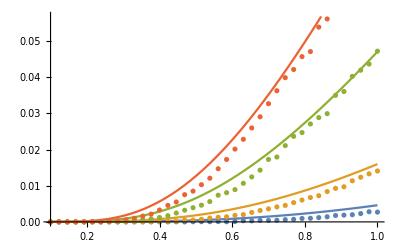

```mathematica
Show[{Plot[{Subscript[J, subn]/.{κ->1},Subscript[J, subn]/.{κ->2},Subscript[J, subn]/.{κ->5},Subscript[J, subn]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1},Transpose@{tvals,-v2},Transpose@{tvals,-v5},Transpose@{tvals,-v10}}]}]
```

```mathematica
v1t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k1_t0.h5","vvals"];
```

```mathematica
v2t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k2_t0.h5","vvals"];
```

```mathematica
v5t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k5_t0.h5","vvals"];
```

```mathematica
v10t0 = Import["/home/ieshghi/Documents/code/dumbbell/data/temp_runs/decoup_k10_t0.h5","vvals"];
```

General::munfl: Exp[-2019.63] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1019.81] is too small to represent as a normalized machine number; precision may be lost.

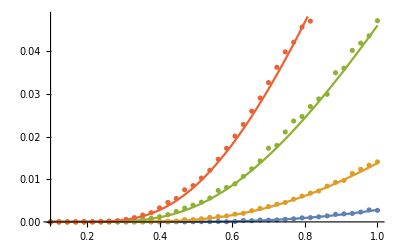

```mathematica
Show[{Plot[{Subscript[J, subz]/.{κ->1},Subscript[J, subz]/.{κ->2},Subscript[J, subz]/.{κ->5},Subscript[J, subz]/.{κ->10}},{T,0.1,1}],ListPlot[{Transpose@{tvals,-v1t0},Transpose@{tvals,-v2t0},Transpose@{tvals,-v5t0},Transpose@{tvals,-v10t0}}]}]
```